{{x→-1,y→3}}

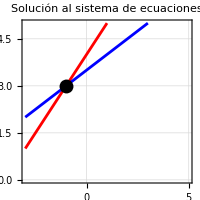

```mathematica
eq1 = 2 x - 2 y == -8;
eq2 =-2x + 4 y == 14;
sol = Solve[ {eq1, eq2}, {x, y}]
ContourPlot[Evaluate@{eq1,eq2},{x,-3,5},{y,0,5},ContourStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}},ImageSize->200,Epilog->{Black,PointSize[.05],Point[{x,y}/. First@sol]},GridLines->Automatic,PlotLabel->"Solución al sistema de ecuaciones"]
```

{{y→2-x}}

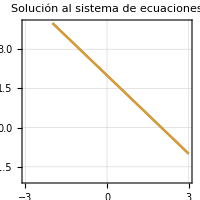

```mathematica
eq3 =  x + y == 2;
eq4 =2x + 2 y == 4;
sol = Solve[ {eq3, eq4}, {x, y}]
ContourPlot[Evaluate@{eq3,eq4},{x,-3,3},{y,-2, 4},GridLines->Automatic,PlotLabel->"Solución al sistema de ecuaciones"]
```

{}

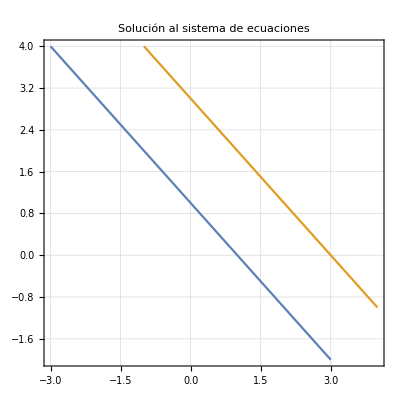

```mathematica
eq5 = x + y == 1;
eq6 = x + y == 3;
sol = Solve[ {eq5, eq6}, {x, y}]
ContourPlot[Evaluate@{eq5,eq6},{x,-3,4},{y,-2, 4},GridLines->Automatic,PlotLabel->"Solución al sistema de ecuaciones"]
```

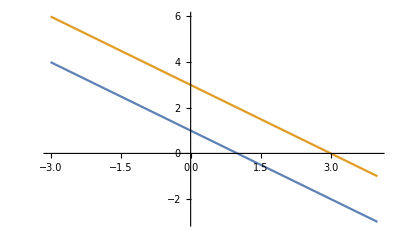

```mathematica
Plot[{-x+1, -x+3},{x, -3, 4}]
```

```mathematica
eq7=7x-15y ==1;
eq8=-x-6y==8;
sol = Solve[ {eq7, eq8}, {x, y}]
```

{{x→-2,y→-1}}

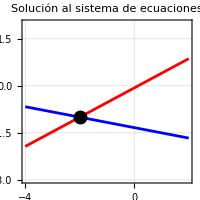

```mathematica
ContourPlot[Evaluate@{eq7,eq8},{x,-4,2},{y,-3,2},ContourStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}},ImageSize->200,Epilog->{Black,PointSize[.05],Point[{x,y}/. First@sol]},GridLines->Automatic,PlotLabel->"Solución al sistema de ecuaciones"]
```

```mathematica
eq9=(3x)/2+y==11;
eq10=x + y/2==7;
sol=Solve[{eq9, eq10},{x, y}]
```

{{x→6,y→2}}

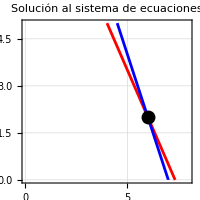

```mathematica
ContourPlot[Evaluate@{eq9,eq10},{x,0,8},{y,0,5},ContourStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}},ImageSize->200,Epilog->{Black,PointSize[.05],Point[{x,y}/. First@sol]},GridLines->Automatic,PlotLabel->"Solución al sistema de ecuaciones"]
```

{{x→4,y→9}}

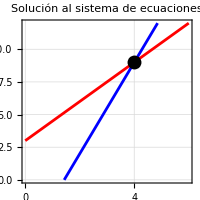

```mathematica
eq11=3(x+2)== 2y;
eq12 = 2 (y+5) == 7x;
sol=Solve[{eq11, eq12},{x, y}]
ContourPlot[Evaluate@{eq11,eq12},{x,0,6},{y,0,12},ContourStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}},ImageSize->200,Epilog->{Black,PointSize[.05],Point[{x,y}/. First@sol]},GridLines->Automatic,PlotLabel->"Solución al sistema de ecuaciones"]
```